```mathematica
1+1
```

2

```mathematica
fD1 = Import["D:\\Kami\\git_folder\\notes_5sem\\rqc\\data_processing_1\\D1_v1.csv"];
fD2 = Import["D:\\Kami\\git_folder\\notes_5sem\\rqc\\data_processing_1\\D2_v1.csv"];
fD1 = Flatten@fD1;
fD2 = Flatten@fD2;
```

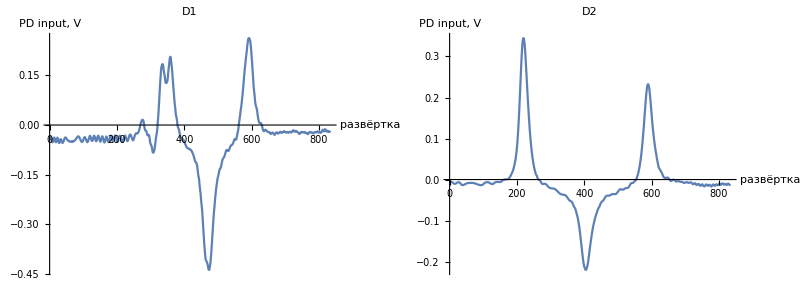

```mathematica
scale = 240;
image = Multicolumn[{
ListPlot[fD1, PlotRange->Full, Joined->True, ImageSize->{scale, scale}, AspectRatio->1,
PlotLabel->"D1", AxesLabel->{"развёртка", "PD input, V"}],
ListPlot[fD2, PlotRange->Full, Joined->True, ImageSize->{scale, scale}, AspectRatio->1,
PlotLabel->"D2", AxesLabel->{"развёртка", "PD input, V"}]
}]
```

```mathematica
(* отнормируем *)
αx = 10. /Length@fD1
xs =αx Range[Length@fD1] ;
data = Transpose[{xs, Flatten@fD1}];
```

0.0119904

```mathematica
color1 = RGBColor[0.27,0.25,1.]
```

RGBColor[0.27, 0.25, 1.]

## Подготовка

```mathematica
d1 = 200;
d2 = 400;
d3 = 550;
d4 = 650;
```

{a1→0.209984,x01→4.01515,σ1→0.0871442,a2→0.237633,x02→4.30228,σ2→0.123213,c→-0.0439162}

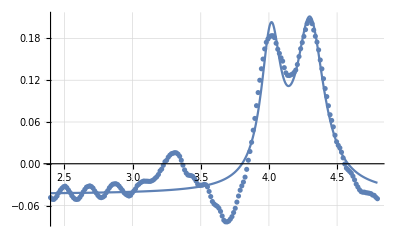

```mathematica
si = d1;
ei = d2;
fit = FindFit[data⟦si;;ei⟧, {a1 σ1^2/((x-x01)^2+σ1^2) +a2 σ2^2/((x-x02)^2+σ2^2) + c}, 
{{a1, 0.15}, {x01, 4}, {σ1, 0.12},{a2, 0.18}, {x02, 4.35}, {σ2, 0.12}, c}, x]
{aV11, x0V11, σV11, aV12, x0V12, σV12, cV1} = {a1, x01, σ1,a2, x02, σ2, c}/.fit;
f1[x_] := aV11 σV11^2/((x-x0V11)^2+σV11^2) +aV12 σV12^2/((x-x0V12)^2+σV12^2) + cV1;
Show[{
Plot[f1[x], {x, data⟦si⟧⟦1⟧, data⟦ei⟧⟦1⟧}, PlotRange->All, GridLines->Automatic],
ListPlot[data⟦si;;ei⟧, PlotRange->All]
}]
```

{a→-0.421719,x0→5.6481,σ→0.239563,c→-0.025222}

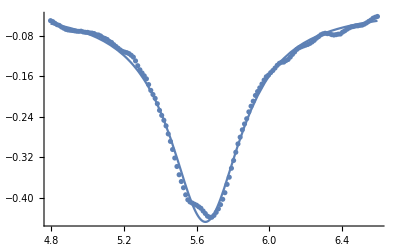

```mathematica
si = d2;
ei = d3;
fit = FindFit[data⟦si;;ei⟧, {a σ^2/((x-x0)^2+σ^2) + c}, {{a, -0.4}, {x0, 5.7}, {σ,0.5}, c}, x]
{aV2, x0V2, σV2, c2V2} = {a, x0, σ, c}/.fit;
f2[x_] := aV2 σV2^2/((x-x0V2)^2+σV2^2) + c2V2;
Show[{
Plot[f2[x], {x, data⟦si⟧⟦1⟧, data⟦ei⟧⟦1⟧}, PlotRange->All],
ListPlot[data⟦si;;ei⟧, PlotRange->All]
}]
```

{a→0.332879,x0→7.09455,σ→0.196566,c2→-0.0628763}

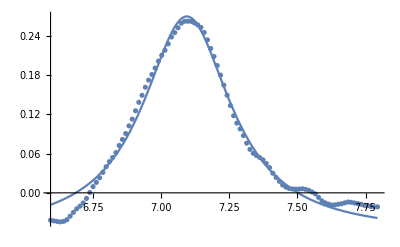

```mathematica
si = d3;
ei = d4;
fit = FindFit[data⟦si;;ei⟧, {a σ^2/((x-x0)^2+σ^2) + c2}, {{a, 0.37}, {x0, 7}, {σ, 0.135}, c2}, x]
{aV3, x0V3, σV3, c2V3} = {a, x0, σ, c2}/.fit;
f3[x_] := aV3 σV3^2/((x-x0V3)^2+σV3^2) + c2V3;
Show[{
Plot[f3[x], {x, data⟦si⟧⟦1⟧, data⟦ei⟧⟦1⟧}, PlotRange->All],
ListPlot[data⟦si;;ei⟧, PlotRange->All]
}]
```

## Фит

{a11→0.206141,x011→4.01259,σ11→0.0845144,a12→0.242205,x012→4.30355,σ12→0.138371,a2→-0.412799,x02→5.64942,σ2→0.2402,a3→0.325658,x03→7.09096,σ3→0.181521,c→-0.0404372}

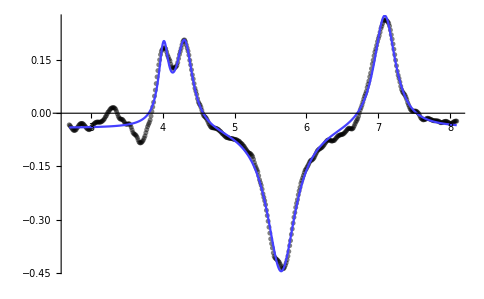

```mathematica
si = 225;
ei = 675;
nlm = NonlinearModelFit[data⟦si;;ei⟧, 
a11 σ11^2/((x-x011)^2+σ11^2)+a12 σ12^2/((x-x012)^2+σ12^2)+a2 σ2^2/((x-x02)^2+σ2^2)+a3 σ3^2/((x-x03)^2+σ3^2)+ c, 
{{a11, aV11}, {x011, x0V11}, {σ11, σV11},
{a12, aV12}, {x012, x0V12}, {σ12, σV12},
{a2, aV2}, {x02, x0V2}, {σ2,σV2},
{a3, aV3}, {x03, x0V3}, {σ3, σV3}, c},x];
fit0 = nlm["BestFitParameters"]
f0[x_] :=a11 σ11^2/((x-x011)^2+σ11^2)+a12 σ12^2/((x-x012)^2+σ12^2)+a2 σ2^2/((x-x02)^2+σ2^2)+a3 σ3^2/((x-x03)^2+σ3^2)+ c /. fit0;
im1 = Show[{
ListPlot[data⟦si;;ei⟧, PlotRange->All, Joined->False, PlotStyle->{Black, Opacity[0.5]}],
Plot[f0[x], {x, data⟦si⟧⟦1⟧, data⟦ei⟧⟦1⟧}, PlotRange->All, PlotStyle->color1]
}]
```

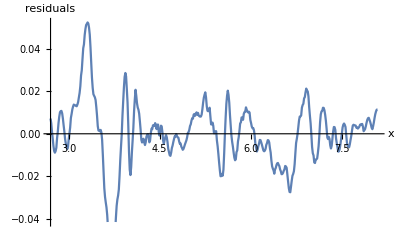

```mathematica
im2 = ListPlot[Transpose[{xs⟦si;;ei⟧,nlm["FitResiduals"]}], Joined->True, AxesLabel->{"x", "residuals"}, PlotRange->{{si αx, ei αx}, Automatic}]
```

```mathematica
nlm["ParameterTable"]
```

General::munfl: Exp[-1790.36] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1734.98] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2065.62] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
a11 | 0.206141 | 0.00738083 | 27.9292 | 2.51185×10^-99
x011 | 4.01259 | 0.00324173 | 1237.79 | 0.
σ11 | 0.0845144 | 0.00559498 | 15.1054 | 8.49255×10^-42
a12 | 0.242205 | 0.00566588 | 42.748 | 2.15735×10^-158
x012 | 4.30355 | 0.00394559 | 1090.72 | 0.
σ12 | 0.138371 | 0.00645871 | 21.4239 | 3.537×10^-70
a2 | -0.412799 | 0.0042596 | -96.9101 | 5.11228×10^-298
x02 | 5.64942 | 0.00243435 | 2320.71 | 0.
σ2 | 0.2402 | 0.00408351 | 58.8218 | 4.95449×10^-210
a3 | 0.325658 | 0.00484663 | 67.1927 | 8.13375×10^-233
x03 | 7.09096 | 0.00267594 | 2649.9 | 0.
σ3 | 0.181521 | 0.00438534 | 41.3926 | 1.77591×10^-153
c | -0.0404372 | 0.00162329 | -24.9106 | 5.86411×10^-86

## Обработка

```mathematica
Print["Отклонение CR: ", Abs@((x03 + (x011+x012)/2)/2 - x02)/x02 * 100 /. fit0, "%"]
```

Отклонение CR: 0.440798%

```mathematica
dots2freq =  (803.5)/ (x03 - (x011+x012)/2) /. fit0
(* расстояние между Ia и Ib *)
(x012-x011)dots2freq/. fit0
```

273.961

79.7124

```mathematica
σerrs = nlm["ParameterErrors"]⟦{3, 6, 9, 12}⟧ 
Print["FWHM Ia:   ", 2Abs[σ11] dots2freq /. fit0,"±",  dots2freq σerrs⟦1⟧, " МГц"]
Print["FWHM Ib:   ", 2Abs[σ12] dots2freq /. fit0,"±",  dots2freq σerrs⟦2⟧, " МГц"]
Print["FWHM II:   ", 2Abs[σ2] dots2freq /. fit0,"±",  dots2freq σerrs⟦3⟧, " МГц"]
Print["FWHM III:  ",2 Abs[σ3] dots2freq /. fit0,"±",  dots2freq σerrs⟦4⟧, " МГц"]
```

{0.00559498,0.00645871,0.00408351,0.00438534}

FWHM Ia:   46.3073±1.53281 МГц

FWHM Ib:   75.8163±1.76943 МГц

FWHM II:   131.611±1.11872 МГц

FWHM III:  99.4591±1.20141 МГц

```mathematica
(* ±% от scale err *)
(Plus@@nlm["ParameterErrors"]⟦{2,8}⟧/ (x03 - (x011+x012)/2) /. fit0)100
```

0.193531

```mathematica
nlm["BestFitParameters"]
```

{a11→0.206141,x011→4.01259,σ11→0.0845144,a12→0.242205,x012→4.30355,σ12→0.138371,a2→-0.412799,x02→5.64942,σ2→0.2402,a3→0.325658,x03→7.09096,σ3→0.181521,c→-0.0404372}

```mathematica
Plus@@(nlm["ParameterErrors"]⟦{2, 5}⟧{x011, x012} /. fit0)
```

0.0299877

## Графики

```mathematica
<< MaTeX`
```

```mathematica
si = 200;
ei = 700;
```

```mathematica
max = Max@fD2;
Ial = dots2freq(x011-σ11 /. fit0);
Iar = dots2freq(x011+σ11 /. fit0);
Iah = f0[x011/. fit0]/2/max;
Ibl = dots2freq(x012-σ12 /. fit0);
Ibr = dots2freq(x012+σ12 /. fit0);
Ibh = f0[x012/. fit0]/2/max;
IIl = dots2freq(x02-σ2 /. fit0);
IIr = dots2freq(x02+σ2 /. fit0);
IIh = f0[x02/. fit0]/2/max;
IIIl = dots2freq(x03-σ3 /. fit0);
IIIr = dots2freq(x03+σ3 /. fit0);
IIIh = f0[x03/. fit0]/2/max;
```

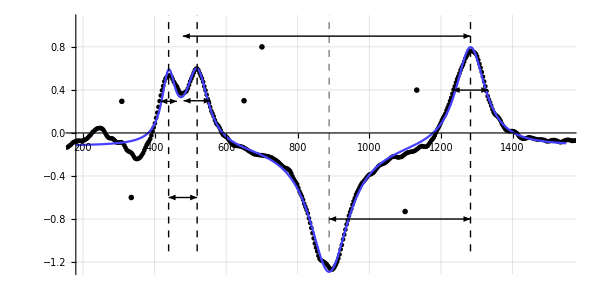

D:\Kami\git_folder\notes_5sem\rqc\data_processing_1\exp_D1.pdf

```mathematica
ArrowSize = 1.2 10^-2;
size1 = 300;
shift = 660;
im1 = Show[{
ListPlot[Map[#+{-shift, 0}&, data⟦si;;ei⟧.{{dots2freq,0},{0,1/max}}], PlotRange->{{180, 1550}, {Full, 1.05}}, Joined->False, PlotStyle->{Black}, AxesLabel->{MaTeX@"\\text{MHz}",MaTeX@"\\text{signal}"},
ImageSize->{2 size1,  size1}, AspectRatio->1/2, GridLines->Automatic,GridLinesStyle->Opacity[0.1],
Epilog->{
Arrowheads[{-ArrowSize,ArrowSize}], Arrow[{{Ial-shift, Iah}, {Iar-shift, Iah}}],
Arrowheads[{-ArrowSize,ArrowSize}], Arrow[{{Ibl-shift, Ibh}, {Ibr-shift, Ibh}}],
Arrowheads[{-ArrowSize,ArrowSize}], Arrow[{{(Ial+Iar)/2-shift, -0.6}, {(Ibl+Ibr)/2-shift, -0.6}}],
Arrowheads[{-ArrowSize,ArrowSize}], Arrow[{{IIIl-shift, IIIh}, {IIIr-shift, IIIh}}],
Arrowheads[{-ArrowSize,ArrowSize}], Arrow[{{(Ial+Iar + Ibl + Ibr)/4-shift, +0.9}, {(IIIl+IIIr)/2-shift, +0.9}}],
Arrowheads[{-ArrowSize,ArrowSize}], Arrow[{{(IIl+IIr)/2-shift, -0.8}, {(IIIl+IIIr)/2-shift, -0.8}}],
{Dashed, Line[{{(Ial+Iar)/2-shift, -1.1}, {(Ial+Iar)/2-shift, +1.1}}]},
{Dashed, Line[{{(Ibl+Ibr)/2-shift, -1.1}, {(Ibl+Ibr)/2-shift, +1.1}}]},
{Dashed, Opacity[0.5], Line[{{(IIl+IIr)/2-shift, -1.1}, {(IIl+IIr)/2-shift, +1.1}}]},
{Dashed, Line[{{(IIIl+IIIr)/2-shift, -1.1}, {(IIIl+IIIr)/2-shift, +1.1}}]},
Text[MaTeX["804 \\pm 18 \\text{ MHz}"], {700, 0.8}],
Text[MaTeX[ToString[Round[(x03-x02 /. fit0) dots2freq, 1]]<>" \\pm 3 \\text{ MHz}"], {1100, -0.73}],
Text[MaTeX[ToString[Round[(x012-x011 /. fit0) dots2freq+7, 1]]<>" \\pm 1 \\text{ MHz}"], {335, -0.6}],
Text[MaTeX[ToString[Round[2Abs@(σ11/. fit0) dots2freq, 1]]<>" \\pm 3 \\text{ MHz}"], {0.9Ial-shift, Iah}],
Text[MaTeX[ToString[Round[2Abs@(σ12/. fit0) dots2freq, 1]]<>" \\pm 3 \\text{ MHz}"], {650, Ibh}],
Text[MaTeX[ToString[Round[2Abs@(σ3/. fit0) dots2freq, 1]]<>" \\pm 4 \\text{ MHz}"], {0.85( IIIr-shift), IIIh}],
}],
Plot[f0[(x+shift)/dots2freq]/max, {x, 180,1550}, PlotRange->All, PlotStyle->color1]
}]
Export[NotebookDirectory[]<>"exp_D1.pdf", im1]
```

```mathematica
0.04 80
```

3.2

```mathematica
dots2freq
```

273.961

```mathematica
(x03-x02 /. fit0) dots2freq
```

394.928

```mathematica
1500-200
```

1300

```mathematica
MaTeX["a"]
```

-Graphics-